## First we start with code

```mathematica
DefineOrLoad2[symbol_,op_]:=Block[{fileName="d:\\saved\\symbols\\"<> symbol<>".m",result},
If[FileExistsQ[fileName],
result=Get[fileName],
result=op[];
Put[result,fileName];
];
result
]
```

```mathematica
SaveSymbol[name_,value_]:=Block[{fileName="d:\\saved\\symbols\\"<> name<>".m",result},
PrintTemporary["Saving "<> fileName];
Put[value,fileName];
]
```

```mathematica
ByCount=DefineOrLoad2["ByCount",Block[{result=Association[],max=398438,n},Monitor[
For[n=1,n<=max,n++,
With[{g=ReadGrof[n]},
With[{count=VertexCount[g]},
If[KeyExistsQ[result,count],result[count]=Append[result[count],n],result[count]={n}]
]
]
],{ProgressIndicator[n,{1,max}],Round[n/max*100,.001]}];
result
]&
];Length[ByCount]
```

11

```mathematica
Map[Length,ByCount]
```

<|4→1,5→1,6→2,7→5,8→14,9→50,10→233,11→1249,12→7595,13→49566,14→339722|>

```mathematica
FindFullFormula[g_]:=Block[{},
FindFullFormula[g,Table[{v},{v,VertexList[g]}]]
]
```

```mathematica
FindFullFormula[g_,v_]:=Block[{edge,pos1,pos2,v2,result={}},
If[CompleteGraphQ[g],
result={SetsToSymbol2[Sort[Map[Sort[#]&,v],#1[[1]]<#2[[1]]&]]}
,
edge=First[EdgeList[GraphComplement[g]]];
Table[If[MemberQ[v[[k]],edge[[1]]],pos1=k],{k,Length[v]}];
Table[If[MemberQ[v[[k]],edge[[2]]],pos2=k],{k,Length[v]}];
v2=v;
v2[[pos1]]=Join[v2[[pos1]],v2[[pos2]]];
v2=Delete[v2,pos2];
result=Join[
FindFullFormula[EdgeAdd[g,edge],v],
FindFullFormula[VertexContract[g,{edge[[1]],edge[[2]]}],v2]
]
];
result
]
```

```mathematica
CalcFormulaeForGrof[n_]:=Block[{},DefineOrLoad2["\\GrofFormulae\\"<>ToString[n],FindFullFormula[ReadGrof[n]]&]]
```

```mathematica
CalcFormulaeForSet[keys_]:=Block[{n, pos, current, length,block,blockMax,blockResult, some,blockSize=$KernelCount*10,currentTime="unknown", totalTime=0, started,ending},
some={};
length=Length[keys];
PrintTemporary[{length, "items to go"}];
started=DateObject[];
Monitor[
For[pos=1,pos<=length,pos+=blockSize,
blockMax=Min[pos+blockSize-1,length];
block=Take[keys,{pos,blockMax}];
currentTime=First[AbsoluteTiming[
blockResult=ParallelTable[
CalcFormulaeForGrof[n]
,{n,block}]
]];
totalTime+=currentTime;
ending=DatePlus[started,{(totalTime/pos)*length,"Second"}];
current =DeleteDuplicates[Flatten[blockResult,1]];
some=DeleteDuplicates[Join[some,current]];
],
{ProgressIndicator[pos,{1,length}],Round[(pos/length)*100,.001],pos,length, currentTime, totalTime, ending}
];
some
]
```

```mathematica
SymbolsByCount=DefineOrLoad2["SymbolsByCount",Block[{result=Association[]},Table[result[k]=CalcFormulaeForSet[ByCount[k]],{k,4,5}];result]&]
```

<|4→{v1x2x3x4},7,12→{v1x2x3x4x5x6x7x8x9xaxbxc,v1x2x3x45x6x7x8x9xaxbxc,v1x2x3x4x5x6x7x8x9xacxb,v1x2x3x45x6x7x8x9xacxb,v1x2x3x4cx5x6x7x8x9xaxb,v1x2x3x4x5x6x7x8cx9xaxb,v1x2x3x45x6x7x8cx9xaxb,v1x2x3x4x5x6cx7x8x9xaxb,v1x2x3x45x6cx7x8x9xaxb,v1x2x3x4x5x6x7x8x9axbxc,v1x2x3x45x6x7x8x9axbxc,v1x2x3x4cx5x6x7x8x9axb,v1x2x3x4x5x6x7x8cx9axb,v1x2x3x45x6x7x8cx9axb,v1x2x3x4x5x6cx7x8x9axb,v1x2x3x45x6cx7x8x9axb,1165342,v1689x247cx3x5xaxb,v1689x24ax3x5x7cxb,v19abx247cx3x5x68,v1689x247cx3x5xab,v1689x24ax3x5x7bxc,v1689x24ax3x5x7bc,v19x24acx3x5x68x7b,v1689x24acx3x5x7b,v19abcx2467x3x5x8,v19x24acx3x5x678xb,v19bx24acx3x5x678,v19ax24678x3x5xbxc,v19ax24678x3x5xbc,v19acx24678x3x5xb,v19abx24678x3x5xc,v19abcx24678x3x5}|>
 |  |  |  |

```mathematica
SymbolsByCount[13]={{6,3,2,1,1},{5,1,1,1,1,1,1,1,1},{5,2,2,1,1,1,1},{2,1,1,1,1,1,1,1,1,1,1,1},{7,2,2,1,1},{2,2,2,1,1,1,1,1,1,1},{4,2,2,1,1,1,1,1},{4,1,1,1,1,1,1,1,1,1},{5,5,2,1},{6,4,2,1},{3,3,3,2,2},{3,3,3,3,1},{3,2,1,1,1,1,1,1,1,1},{6,4,1,1,1},{4,2,2,2,2,1},{4,3,3,1,1,1},{6,2,1,1,1,1,1},{5,2,2,2,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1},{5,2,2,2,2},{5,3,1,1,1,1,1},{6,3,1,1,1,1},{4,2,2,2,1,1,1},{4,2,1,1,1,1,1,1,1},{3,3,3,2,1,1},{4,4,2,1,1,1},{4,3,3,3},{5,3,3,2},{6,3,2,2},{4,4,3,2},{2,2,2,2,1,1,1,1,1},{7,2,2,2},{7,1,1,1,1,1,1},{3,2,2,2,1,1,1,1},{6,3,3,1},{4,3,1,1,1,1,1,1},{3,3,2,2,2,1},{6,2,2,2,1},{4,3,2,2,2},{2,2,2,2,2,2,1},{3,3,1,1,1,1,1,1,1},{5,3,2,1,1,1},{6,5,1,1},{5,5,3},{4,3,2,2,1,1},{4,4,1,1,1,1,1},{4,3,2,1,1,1,1},{4,4,2,2,1},{4,4,4,1},{3,3,2,1,1,1,1,1},{5,4,4},{5,3,3,1,1},{5,5,1,1,1},{5,2,1,1,1,1,1,1},{4,3,3,2,1},{7,2,1,1,1,1},{6,1,1,1,1,1,1,1},{3,3,2,2,1,1,1},{4,4,3,1,1},{3,2,2,2,2,1,1},{3,1,1,1,1,1,1,1,1,1,1},{5,4,2,2},{2,2,2,2,2,1,1,1},{7,3,1,1,1},{3,2,2,1,1,1,1,1,1},{3,2,2,2,2,2},{5,3,2,2,1},{2,2,1,1,1,1,1,1,1,1,1},{6,2,2,1,1,1},{3,3,3,1,1,1,1},{5,4,2,1,1},{5,4,3,1},{5,4,1,1,1,1}}
```

{{6,3,2,1,1},{5,1,1,1,1,1,1,1,1},{5,2,2,1,1,1,1},{2,1,1,1,1,1,1,1,1,1,1,1},{7,2,2,1,1},{2,2,2,1,1,1,1,1,1,1},{4,2,2,1,1,1,1,1},{4,1,1,1,1,1,1,1,1,1},{5,5,2,1},{6,4,2,1},{3,3,3,2,2},{3,3,3,3,1},{3,2,1,1,1,1,1,1,1,1},{6,4,1,1,1},{4,2,2,2,2,1},{4,3,3,1,1,1},{6,2,1,1,1,1,1},{5,2,2,2,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1},{5,2,2,2,2},{5,3,1,1,1,1,1},{6,3,1,1,1,1},{4,2,2,2,1,1,1},{4,2,1,1,1,1,1,1,1},{3,3,3,2,1,1},{4,4,2,1,1,1},{4,3,3,3},{5,3,3,2},{6,3,2,2},{4,4,3,2},{2,2,2,2,1,1,1,1,1},{7,2,2,2},{7,1,1,1,1,1,1},{3,2,2,2,1,1,1,1},{6,3,3,1},{4,3,1,1,1,1,1,1},{3,3,2,2,2,1},{6,2,2,2,1},{4,3,2,2,2},{2,2,2,2,2,2,1},{3,3,1,1,1,1,1,1,1},{5,3,2,1,1,1},{6,5,1,1},{5,5,3},{4,3,2,2,1,1},{4,4,1,1,1,1,1},{4,3,2,1,1,1,1},{4,4,2,2,1},{4,4,4,1},{3,3,2,1,1,1,1,1},{5,4,4},{5,3,3,1,1},{5,5,1,1,1},{5,2,1,1,1,1,1,1},{4,3,3,2,1},{7,2,1,1,1,1},{6,1,1,1,1,1,1,1},{3,3,2,2,1,1,1},{4,4,3,1,1},{3,2,2,2,2,1,1},{3,1,1,1,1,1,1,1,1,1,1},{5,4,2,2},{2,2,2,2,2,1,1,1},{7,3,1,1,1},{3,2,2,1,1,1,1,1,1},{3,2,2,2,2,2},{5,3,2,2,1},{2,2,1,1,1,1,1,1,1,1,1},{6,2,2,1,1,1},{3,3,3,1,1,1,1},{5,4,2,1,1},{5,4,3,1},{5,4,1,1,1,1}}

```mathematica
CloseKernels[]
```

{}

```mathematica
LaunchKernels[]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local]}

```mathematica
Table[If[!KeyExistsQ[SymbolsByCount,k],SymbolsByCount[k]=CalcFormulaeForSet[ByCount[k]];SaveSymbol["SymbolsByCount",SymbolsByCount]],{k,4,12}]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Length[SymbolsByCount]
```

10

```mathematica
totalDone=0;
```

```mathematica
localDone=0;
```

```mathematica
DistributeDefinitions[localDone]
```

{localDone}

```mathematica
ParallelEvaluate[localDone=0]
```

{0,0,0,0,0,0}

```mathematica
InspectLevel[k_]:=Block[{all, todo=SymbolsByCount[k], todoParts, syms, parts, byRank=Association[], level,pos, sym, sympos, sets, type},
Table[
byRank[rank]={}
,{rank,k}];
PrintTemporary["Total to do ",Length[todo]];
SetSharedVariable[totalDone];
localDone=0;
totalDone=0;
    DistributeDefinitions[localDone];
ParallelEvaluate[localDone=0];
totalDone=0;
PrintTemporary["Converting ",Length[todo]];
Monitor[
todoParts=ParallelMap[Block[{},localDone++;If[localDone==3,totalDone+=localDone;localDone=0];PartitionType[SymbolToSets[#]]]&,todo],
{"converting",ProgressIndicator[totalDone,{1,Length[todo]}],totalDone,Length[todo]}];

PrintTemporary["Splitting ",Length[todo]];
Monitor[
For[pos=1,pos<=Length[todoParts],pos++,
sets=todoParts[[pos]];
level=Length[sets];
byRank[level]=Append[byRank[level],sets]
],
{"splitting",ProgressIndicator[pos,{1,Length[todo]}],pos,Length[todo]}
];
(* filter*)
Table[
byRank[rank]=DeleteDuplicates[byRank[rank]]
,{rank,k}
];
Monitor[
ParallelTable[
all=IntegerPartitions[k,{rank}];
syms=byRank[rank];
PrintTemporary[{Length[syms]," at rank", rank}];
parts=Association[];
For [sympos=1,sympos≤ Length[syms],sympos++,
type=syms[[sympos]];
parts[type]=1
];
Labeled[
Grid[
Table[
If[KeyExistsQ[parts,row],Map[Style[#,Darker[Green]]&,row],Map[Style[#,Red]&,row]],{row,all}
],
Frame->All
],
rank
]
,{rank,k}
],
{rank,k}
]
]
```

## Warning this is computation

```mathematica
InspectLevel[10]
```

{0, at rank,1}

{2, at rank,3}

{6, at rank,5}

{3, at rank,7}

{1, at rank,9}

{1, at rank,10}

{0, at rank,2}

{6, at rank,4}

{5, at rank,6}

{2, at rank,8}

{101,9 | 1
8 | 2
7 | 3
6 | 4
5 | 52,8 | 1 | 1
7 | 2 | 1
6 | 3 | 1
6 | 2 | 2
5 | 4 | 1
5 | 3 | 2
4 | 4 | 2
4 | 3 | 33,7 | 1 | 1 | 1
6 | 2 | 1 | 1
5 | 3 | 1 | 1
5 | 2 | 2 | 1
4 | 4 | 1 | 1
4 | 3 | 2 | 1
4 | 2 | 2 | 2
3 | 3 | 3 | 1
3 | 3 | 2 | 24,6 | 1 | 1 | 1 | 1
5 | 2 | 1 | 1 | 1
4 | 3 | 1 | 1 | 1
4 | 2 | 2 | 1 | 1
3 | 3 | 2 | 1 | 1
3 | 2 | 2 | 2 | 1
2 | 2 | 2 | 2 | 25,5 | 1 | 1 | 1 | 1 | 1
4 | 2 | 1 | 1 | 1 | 1
3 | 3 | 1 | 1 | 1 | 1
3 | 2 | 2 | 1 | 1 | 1
2 | 2 | 2 | 2 | 1 | 16,4 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 1 | 1 | 1 | 17,3 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1 | 1 | 1 | 18,2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19,1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 110}

```mathematica
Print[totalDone]
```

0

```mathematica
InspectLevel[12]
```

{0, at rank,1}

{3, at rank,3}

{11, at rank,5}

{7, at rank,7}

{3, at rank,9}

{1, at rank,11}

{0, at rank,2}

{10, at rank,4}

{10, at rank,6}

{5, at rank,8}

{2, at rank,10}

{1, at rank,12}

{121,11 | 1
10 | 2
9 | 3
8 | 4
7 | 5
6 | 62,10 | 1 | 1
9 | 2 | 1
8 | 3 | 1
8 | 2 | 2
7 | 4 | 1
7 | 3 | 2
6 | 5 | 1
6 | 4 | 2
6 | 3 | 3
5 | 5 | 2
5 | 4 | 3
4 | 4 | 43,9 | 1 | 1 | 1
8 | 2 | 1 | 1
7 | 3 | 1 | 1
7 | 2 | 2 | 1
6 | 4 | 1 | 1
6 | 3 | 2 | 1
6 | 2 | 2 | 2
5 | 5 | 1 | 1
5 | 4 | 2 | 1
5 | 3 | 3 | 1
5 | 3 | 2 | 2
4 | 4 | 3 | 1
4 | 4 | 2 | 2
4 | 3 | 3 | 2
3 | 3 | 3 | 34,8 | 1 | 1 | 1 | 1
7 | 2 | 1 | 1 | 1
6 | 3 | 1 | 1 | 1
6 | 2 | 2 | 1 | 1
5 | 4 | 1 | 1 | 1
5 | 3 | 2 | 1 | 1
5 | 2 | 2 | 2 | 1
4 | 4 | 2 | 1 | 1
4 | 3 | 3 | 1 | 1
4 | 3 | 2 | 2 | 1
4 | 2 | 2 | 2 | 2
3 | 3 | 3 | 2 | 1
3 | 3 | 2 | 2 | 25,7 | 1 | 1 | 1 | 1 | 1
6 | 2 | 1 | 1 | 1 | 1
5 | 3 | 1 | 1 | 1 | 1
5 | 2 | 2 | 1 | 1 | 1
4 | 4 | 1 | 1 | 1 | 1
4 | 3 | 2 | 1 | 1 | 1
4 | 2 | 2 | 2 | 1 | 1
3 | 3 | 3 | 1 | 1 | 1
3 | 3 | 2 | 2 | 1 | 1
3 | 2 | 2 | 2 | 2 | 1
2 | 2 | 2 | 2 | 2 | 26,6 | 1 | 1 | 1 | 1 | 1 | 1
5 | 2 | 1 | 1 | 1 | 1 | 1
4 | 3 | 1 | 1 | 1 | 1 | 1
4 | 2 | 2 | 1 | 1 | 1 | 1
3 | 3 | 2 | 1 | 1 | 1 | 1
3 | 2 | 2 | 2 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 1 | 17,5 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 2 | 1 | 1 | 1 | 1 | 1 | 1
3 | 3 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 2 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 1 | 1 | 1 | 18,4 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 19,3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 110,2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 111,1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 112}

```mathematica
BellB[12]
```

4213597

```mathematica
PartitionsP[12]
```

77

```mathematica
PartitionsP[13]
```

101

## Now the experiments

```mathematica
Keys[ByCount]
```

{4,5,6,7,8,9,10,11,12,13,14}

```mathematica
CalcFormulaeForSet[ByCount[4]]
```

Loading d:\saved\symbols\\GrofFormulae\1.m

{v1x2x3x4}

```mathematica
FindFullFormula[ReadGrof[2]]
```

{v1x2x3x4x5,v14x2x3x5}

```mathematica
CalcFormulaeForSet[ByCount[5]]
```

Saved d:\saved\symbols\\GrofFormulae\2.m

{v1x2x3x4x5,v14x2x3x5}

```mathematica
CalcFormulaeForSet[ByCount[6]]
```

Saved d:\saved\symbols\\GrofFormulae\3.m

Saved d:\saved\symbols\\GrofFormulae\4.m

{v1x2x3x4x5x6,v1x24x3x5x6,v14x2x3x5x6,v16x2x3x4x5,v16x24x3x5,v1x2x36x4x5,v1x25x3x4x6,v1x25x36x4,v14x2x36x5,v14x25x3x6,v14x25x36}

```mathematica
CalcFormulaeForSet[ByCount[7]]
```

{v1x2x3x4x5x6x7,v1x2x3x47x5x6,v1x2x3x4x5x67,v1x24x3x5x6x7,v1x24x3x5x67,v14x2x3x5x6x7,v14x2x3x5x67,v16x2x3x4x5x7,v16x2x3x47x5,v16x24x3x5x7,v15x2x3x4x6x7,v15x2x3x47x6,v15x2x3x4x67,v15x24x3x6x7,v15x24x3x67,v1x2x37x4x5x6,v1x24x37x5x6,v1x25x3x4x6x7,v1x25x3x47x6,v1x25x37x4x6,v14x2x37x5x6,v14x25x3x6x7,v14x25x37x6,v16x2x37x4x5,v16x24x37x5,v16x25x3x4x7,v16x25x3x47,v16x25x37x4,v1x2x35x4x6x7,v1x2x35x4x67,v1x24x35x6x7,v1x24x35x67,v1x27x3x4x5x6,v1x27x35x4x6,v14x2x35x6x7,v14x2x35x67,v14x27x3x5x6,v14x27x35x6,v16x2x35x4x7,v16x24x35x7,v16x27x3x4x5,v16x27x35x4,v1x26x3x4x5x7,v1x26x3x47x5,v14x26x3x5x7,v17x2x3x4x5x6,v147x2x3x5x6,v17x26x3x4x5,v147x26x3x5,v17x24x3x5x6,v1x2x3x4x57x6,v1x24x3x57x6,v14x2x3x57x6,v16x2x3x4x57,v16x24x3x57}

```mathematica
CalcFormulaeForSet[ByCount[8]]//Length
```

328

```mathematica
BellB[8]
```

4140

```mathematica
CalcFormulaeForSet[ByCount[9]]//Length
```

2110

```mathematica
CalcFormulaeForSet[ByCount[10]]//Length
```

16570

```mathematica
CalcFormulaeForSet[ByCount[4]]
```

{v1x2x3x4}

```mathematica
CalcFormulaeForSet[ByCount[11]]//Length
```

135500

```mathematica
BellB[11]
```

678570

```mathematica
BellB[3]
```

5

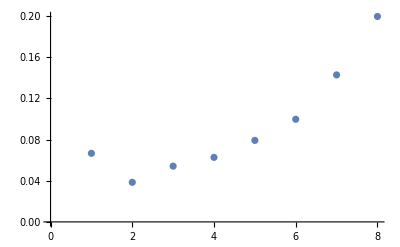

```mathematica
Table[Length[CalcFormulaeForSet[ByCount[k]]]/BellB[k],{k,4,12}]//ListPlot
```

```mathematica
CalcFormulaeForSet[ByCount[12]]//Length
```

1165374

```mathematica
CalcFormulaeForSet[ByCount[13]]//Length
```

```mathematica
CalcFormulaeForSet[ByCount[14]]//Length
```

```mathematica
IntegerPartitions[5,{2}]
```

{{4,1},{3,2}}

## Computations for various vertex counts

```mathematica
InspectLevel[4]
```

{0, at rank,1}

{0, at rank,2}

{0, at rank,3}

{1, at rank,4}

{41,3 | 1
2 | 22,2 | 1 | 13,1 | 1 | 1 | 14}

```mathematica
InspectLevel[5]
```

{0, at rank,1}

{0, at rank,2}

{0, at rank,3}

{1, at rank,4}

{1, at rank,5}

{51,4 | 1
3 | 22,3 | 1 | 1
2 | 2 | 13,2 | 1 | 1 | 14,1 | 1 | 1 | 1 | 15}

```mathematica
InspectLevel[6]
```

{0, at rank,1}

{0, at rank,2}

{1, at rank,3}

{4, at rank,4}

{5, at rank,5}

{1, at rank,6}

{61,5 | 1
4 | 2
3 | 32,4 | 1 | 1
3 | 2 | 1
2 | 2 | 23,3 | 1 | 1 | 1
2 | 2 | 1 | 14,2 | 1 | 1 | 1 | 15,1 | 1 | 1 | 1 | 1 | 16}

```mathematica
InspectLevel[7]
```

{0, at rank,1}

{0, at rank,3}

{12, at rank,4}

{29, at rank,5}

{13, at rank,6}

{1, at rank,7}

{0, at rank,2}

{71,6 | 1
5 | 2
4 | 32,5 | 1 | 1
4 | 2 | 1
3 | 3 | 1
3 | 2 | 23,4 | 1 | 1 | 1
3 | 2 | 1 | 1
2 | 2 | 2 | 14,3 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 15,2 | 1 | 1 | 1 | 1 | 16,1 | 1 | 1 | 1 | 1 | 1 | 17}

```mathematica
InspectLevel[8]
```

{0, at rank,1}

{1, at rank,3}

{149, at rank,5}

{120, at rank,6}

{24, at rank,7}

{1, at rank,8}

{0, at rank,2}

{33, at rank,4}

{81,7 | 1
6 | 2
5 | 3
4 | 42,6 | 1 | 1
5 | 2 | 1
4 | 3 | 1
4 | 2 | 2
3 | 3 | 23,5 | 1 | 1 | 1
4 | 2 | 1 | 1
3 | 3 | 1 | 1
3 | 2 | 2 | 1
2 | 2 | 2 | 24,4 | 1 | 1 | 1 | 1
3 | 2 | 1 | 1 | 1
2 | 2 | 2 | 1 | 15,3 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1 | 16,2 | 1 | 1 | 1 | 1 | 1 | 17,1 | 1 | 1 | 1 | 1 | 1 | 1 | 18}

```mathematica
InspectLevel[9]
```

{0, at rank,1}

{1, at rank,3}

{772, at rank,5}

{294, at rank,7}

{32, at rank,8}

{1, at rank,9}

{0, at rank,2}

{123, at rank,4}

{887, at rank,6}

{91,8 | 1
7 | 2
6 | 3
5 | 42,7 | 1 | 1
6 | 2 | 1
5 | 3 | 1
5 | 2 | 2
4 | 4 | 1
4 | 3 | 2
3 | 3 | 33,6 | 1 | 1 | 1
5 | 2 | 1 | 1
4 | 3 | 1 | 1
4 | 2 | 2 | 1
3 | 3 | 2 | 1
3 | 2 | 2 | 24,5 | 1 | 1 | 1 | 1
4 | 2 | 1 | 1 | 1
3 | 3 | 1 | 1 | 1
3 | 2 | 2 | 1 | 1
2 | 2 | 2 | 2 | 15,4 | 1 | 1 | 1 | 1 | 1
3 | 2 | 1 | 1 | 1 | 1
2 | 2 | 2 | 1 | 1 | 16,3 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1 | 1 | 17,2 | 1 | 1 | 1 | 1 | 1 | 1 | 18,1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19}

```mathematica
InspectLevel[10]
```

{0, at rank,1}

{2, at rank,3}

{6, at rank,5}

{3, at rank,7}

{1, at rank,9}

{1, at rank,10}

{0, at rank,2}

{6, at rank,4}

{5, at rank,6}

{2, at rank,8}

{101,9 | 1
8 | 2
7 | 3
6 | 4
5 | 52,8 | 1 | 1
7 | 2 | 1
6 | 3 | 1
6 | 2 | 2
5 | 4 | 1
5 | 3 | 2
4 | 4 | 2
4 | 3 | 33,7 | 1 | 1 | 1
6 | 2 | 1 | 1
5 | 3 | 1 | 1
5 | 2 | 2 | 1
4 | 4 | 1 | 1
4 | 3 | 2 | 1
4 | 2 | 2 | 2
3 | 3 | 3 | 1
3 | 3 | 2 | 24,6 | 1 | 1 | 1 | 1
5 | 2 | 1 | 1 | 1
4 | 3 | 1 | 1 | 1
4 | 2 | 2 | 1 | 1
3 | 3 | 2 | 1 | 1
3 | 2 | 2 | 2 | 1
2 | 2 | 2 | 2 | 25,5 | 1 | 1 | 1 | 1 | 1
4 | 2 | 1 | 1 | 1 | 1
3 | 3 | 1 | 1 | 1 | 1
3 | 2 | 2 | 1 | 1 | 1
2 | 2 | 2 | 2 | 1 | 16,4 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 1 | 1 | 1 | 17,3 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1 | 1 | 1 | 18,2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19,1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 110}

```mathematica
InspectLevel[11]
```

{0, at rank,1}

{1, at rank,3}

{9, at rank,5}

{5, at rank,7}

{2, at rank,9}

{1, at rank,11}

{0, at rank,2}

{7, at rank,4}

{7, at rank,6}

{3, at rank,8}

{1, at rank,10}

{111,10 | 1
9 | 2
8 | 3
7 | 4
6 | 52,9 | 1 | 1
8 | 2 | 1
7 | 3 | 1
7 | 2 | 2
6 | 4 | 1
6 | 3 | 2
5 | 5 | 1
5 | 4 | 2
5 | 3 | 3
4 | 4 | 33,8 | 1 | 1 | 1
7 | 2 | 1 | 1
6 | 3 | 1 | 1
6 | 2 | 2 | 1
5 | 4 | 1 | 1
5 | 3 | 2 | 1
5 | 2 | 2 | 2
4 | 4 | 2 | 1
4 | 3 | 3 | 1
4 | 3 | 2 | 2
3 | 3 | 3 | 24,7 | 1 | 1 | 1 | 1
6 | 2 | 1 | 1 | 1
5 | 3 | 1 | 1 | 1
5 | 2 | 2 | 1 | 1
4 | 4 | 1 | 1 | 1
4 | 3 | 2 | 1 | 1
4 | 2 | 2 | 2 | 1
3 | 3 | 3 | 1 | 1
3 | 3 | 2 | 2 | 1
3 | 2 | 2 | 2 | 25,6 | 1 | 1 | 1 | 1 | 1
5 | 2 | 1 | 1 | 1 | 1
4 | 3 | 1 | 1 | 1 | 1
4 | 2 | 2 | 1 | 1 | 1
3 | 3 | 2 | 1 | 1 | 1
3 | 2 | 2 | 2 | 1 | 1
2 | 2 | 2 | 2 | 2 | 16,5 | 1 | 1 | 1 | 1 | 1 | 1
4 | 2 | 1 | 1 | 1 | 1 | 1
3 | 3 | 1 | 1 | 1 | 1 | 1
3 | 2 | 2 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 1 | 1 | 17,4 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 1 | 1 | 1 | 1 | 18,3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 19,2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 110,1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 111}

```mathematica
InspectLevel[12]
```

Total to do 1165374

Converting 1165374

## other stuff

```mathematica
$KernelCount
```

0

```mathematica
$KernelCount=8
```

Set::wrsym: Symbol $KernelCount is Protected.

8

```mathematica
LaunchKernels[]
```

LaunchKernels::nodef: Some subkernels are already running. Not launching default kernels again.

$Failed

```mathematica
CloseKernels[]
```

{KernelObject[1,local,<defunct>],KernelObject[2,local,<defunct>],KernelObject[3,local,<defunct>],KernelObject[4,local,<defunct>],KernelObject[5,local,<defunct>],KernelObject[6,local,<defunct>]}

```mathematica
LaunchKernels[]
```

{KernelObject[9,local],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local],KernelObject[13,local],KernelObject[14,local]}

## Now for 13

```mathematica
InspectLevel13[k_]:=Block[{all, todo=SymbolsByCount[k], todoParts, syms, parts, byRank=Association[], level,pos, sym, sympos, sets, type},
Table[
byRank[rank]={}
,{rank,k}];
PrintTemporary["Total to do ",Length[todo]];
SetSharedVariable[totalDone];
localDone=0;
totalDone=0;
    DistributeDefinitions[localDone];
ParallelEvaluate[localDone=0];
totalDone=0;
PrintTemporary["Converting ",Length[todo]];
todoParts=todo;

PrintTemporary["Splitting ",Length[todo]];
Monitor[
For[pos=1,pos<=Length[todoParts],pos++,
sets=todoParts[[pos]];
level=Length[sets];
byRank[level]=Append[byRank[level],sets]
],
{"splitting",ProgressIndicator[pos,{1,Length[todo]}],pos,Length[todo]}
];
(* filter*)
Table[
byRank[rank]=DeleteDuplicates[byRank[rank]]
,{rank,k}
];
Monitor[
ParallelTable[
all=IntegerPartitions[k,{rank}];
syms=byRank[rank];
PrintTemporary[{Length[syms]," at rank", rank}];
parts=Association[];
For [sympos=1,sympos≤ Length[syms],sympos++,
type=syms[[sympos]];
parts[type]=1
];
Labeled[
Grid[
Table[
If[KeyExistsQ[parts,row],Map[Style[#,Darker[Green]]&,row],Map[Style[#,Red]&,row]],{row,all}
],
Frame->All
],
rank
]
,{rank,k}
],
{rank,k}
]
]
```

```mathematica
InspectLevel13[13]
```

{0, at rank,1}

{2, at rank,3}

{12, at rank,4}

{16, at rank,5}

{13, at rank,6}

{11, at rank,7}

{0, at rank,2}

{7, at rank,8}

{5, at rank,9}

{3, at rank,10}

{2, at rank,11}

{1, at rank,12}

{1, at rank,13}

{131,12 | 1
11 | 2
10 | 3
9 | 4
8 | 5
7 | 62,11 | 1 | 1
10 | 2 | 1
9 | 3 | 1
9 | 2 | 2
8 | 4 | 1
8 | 3 | 2
7 | 5 | 1
7 | 4 | 2
7 | 3 | 3
6 | 6 | 1
6 | 5 | 2
6 | 4 | 3
5 | 5 | 3
5 | 4 | 43,10 | 1 | 1 | 1
9 | 2 | 1 | 1
8 | 3 | 1 | 1
8 | 2 | 2 | 1
7 | 4 | 1 | 1
7 | 3 | 2 | 1
7 | 2 | 2 | 2
6 | 5 | 1 | 1
6 | 4 | 2 | 1
6 | 3 | 3 | 1
6 | 3 | 2 | 2
5 | 5 | 2 | 1
5 | 4 | 3 | 1
5 | 4 | 2 | 2
5 | 3 | 3 | 2
4 | 4 | 4 | 1
4 | 4 | 3 | 2
4 | 3 | 3 | 34,9 | 1 | 1 | 1 | 1
8 | 2 | 1 | 1 | 1
7 | 3 | 1 | 1 | 1
7 | 2 | 2 | 1 | 1
6 | 4 | 1 | 1 | 1
6 | 3 | 2 | 1 | 1
6 | 2 | 2 | 2 | 1
5 | 5 | 1 | 1 | 1
5 | 4 | 2 | 1 | 1
5 | 3 | 3 | 1 | 1
5 | 3 | 2 | 2 | 1
5 | 2 | 2 | 2 | 2
4 | 4 | 3 | 1 | 1
4 | 4 | 2 | 2 | 1
4 | 3 | 3 | 2 | 1
4 | 3 | 2 | 2 | 2
3 | 3 | 3 | 3 | 1
3 | 3 | 3 | 2 | 25,8 | 1 | 1 | 1 | 1 | 1
7 | 2 | 1 | 1 | 1 | 1
6 | 3 | 1 | 1 | 1 | 1
6 | 2 | 2 | 1 | 1 | 1
5 | 4 | 1 | 1 | 1 | 1
5 | 3 | 2 | 1 | 1 | 1
5 | 2 | 2 | 2 | 1 | 1
4 | 4 | 2 | 1 | 1 | 1
4 | 3 | 3 | 1 | 1 | 1
4 | 3 | 2 | 2 | 1 | 1
4 | 2 | 2 | 2 | 2 | 1
3 | 3 | 3 | 2 | 1 | 1
3 | 3 | 2 | 2 | 2 | 1
3 | 2 | 2 | 2 | 2 | 26,7 | 1 | 1 | 1 | 1 | 1 | 1
6 | 2 | 1 | 1 | 1 | 1 | 1
5 | 3 | 1 | 1 | 1 | 1 | 1
5 | 2 | 2 | 1 | 1 | 1 | 1
4 | 4 | 1 | 1 | 1 | 1 | 1
4 | 3 | 2 | 1 | 1 | 1 | 1
4 | 2 | 2 | 2 | 1 | 1 | 1
3 | 3 | 3 | 1 | 1 | 1 | 1
3 | 3 | 2 | 2 | 1 | 1 | 1
3 | 2 | 2 | 2 | 2 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 17,6 | 1 | 1 | 1 | 1 | 1 | 1 | 1
5 | 2 | 1 | 1 | 1 | 1 | 1 | 1
4 | 3 | 1 | 1 | 1 | 1 | 1 | 1
4 | 2 | 2 | 1 | 1 | 1 | 1 | 1
3 | 3 | 2 | 1 | 1 | 1 | 1 | 1
3 | 2 | 2 | 2 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 1 | 1 | 18,5 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 19,4 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 110,3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 111,2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 112,1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 113}